```mathematica
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\Direct_Greens_Function\\bin"];
```

```mathematica
gData=Flatten[Import["greens.dat","Table"]];
```

```mathematica
t=1.0;
J=0.4t;
Emin=-6;
Emax=8;
```

```mathematica
iδ=0.05I;
nSteps=1400;
Σ[ω_]:=-4t/Sqrt[3]BesselJ[7/2-ω/J,2Sqrt[3]t/J]/BesselJ[5/2-ω/J,2Sqrt[3]t/J]
Gscba[ω_]:=1/(ω+iδ-2J-Σ[ω+iδ]);
data=Table[(ω=(Emax-Emin)*(it/nSteps)+Emin;Gtemp=Gscba[ω];
StringJoin["(",ToString[DecimalForm[Re[Gtemp]]],",",ToString[DecimalForm[Im[Gtemp]]],")"]
),{it,0,nSteps}];
Export["greens_scba.dat",data,"Table"];
gData=Flatten[Import["greens_scba.dat","Table"]];
```

```mathematica
GF=Table[
(w=(Emax-Emin)*(it-1)/(Length[gData]-1)+Emin;
z=ToExpression[StringJoin["{",StringTake[gData[[it]],{2;;-2}],"}"]];
{w,z[[1]]+I z[[2]]}
),
{it, 1,Length[gData]}];
```

```mathematica
rotGF[GF_,m4_]:=(
d=0.05;
w0=2J;
w=Table[GF[[it,1]],{it,1,Length[GF]}]+I d;
G0=1/(w-w0);
invG0=G0^-1;
invG=GF[[;;,2]]^-1;
EGE=(4t^2)^-1/((invG0-invG)^-1 -(invG0+3invG)^-1);
PGP=(4t^2)^-1/((invG0-invG)^-1 - G0);
NGE=(PGP-EGE)/3;
res=EGE+(Exp[I Pi m4/2]+Exp[I Pi m4]+Exp[3I Pi m4/2])NGE;
Table[{GF[[it,1]],res[[it]]},{it,1,Length[GF]}]
)
```

```mathematica
newGF[GF_,m_]:=(
d=0.05;
w0=2J;
w=Table[GF[[it,1]],{it,1,Length[GF]}]+I d;
G0=1/(w-w0);
invG0=G0^-1;
G=GF[[;;,2]];
invG=G^-1;
Sig0=(invG0-invG)/4;
GEE=(Sig0+Sig0*G*Sig0)/t^2;
GNE=(Sig0*G*Sig0)/t^2;
res=GEE+(Exp[I m Pi/2]+Exp[2I m Pi/2]+Exp[3I m Pi/2])GNE;
Table[{GF[[it,1]],res[[it]]},{it,1,Length[GF]}]
)
```

```mathematica
m=1
```

1

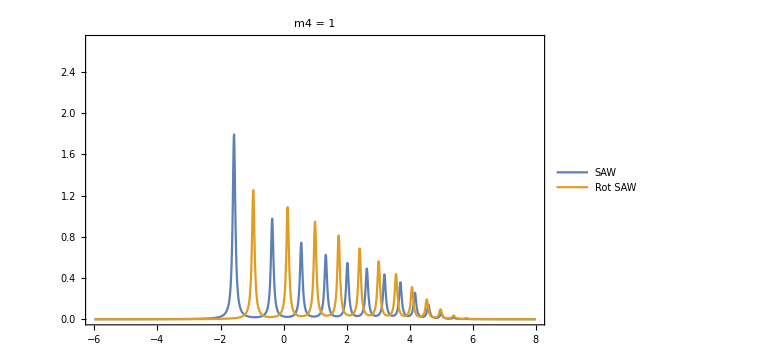

```mathematica
rfig=(
rGF=rotGF[GF,m];
ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{rGF[[it,1]],-Im[rGF[[it,2]]]/Pi},{it,1,Length[rGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style[StringJoin["m4 = ",ToString[m]],20,Black,FontFamily->"Book Oldman Style"]
]
)
```

```mathematica
nfig=(
nGF=newGF[GF,m];
ListLinePlot[{Table[{GF[[it,1]],-Im[GF[[it,2]]]/Pi},{it,1,Length[GF]}],Table[{nGF[[it,1]],-Im[nGF[[it,2]]]/Pi},{it,1,Length[nGF]}]},
PlotRange->{{Emin,Emax},{0,2.7}},Frame->True,Axes->{True,False},ImageSize->Large,
PlotLegends->Placed[{Style["SAW",20,Black,FontFamily->"Book Oldman Style"],Style["Rot SAW",20,Black,FontFamily->"Book Oldman Style"]},{0.8,0.8}],
FrameStyle->Directive[Black, 16],
PlotLabel->Style[StringJoin["m4 = ",ToString[m]],20,Black,FontFamily->"Book Oldman Style"]
]
)
```

-Graphics-